```mathematica
m[f_, k_, n_, str_, a_, b_] := Module[{data1, data2, p1, p2, p3, p4, g},
data1=Import[StringJoin["/Users/yakimkina/_workspace/_mgtu/cpp/solving_interpolation_problems/cmake-build-debug/output/test", ToString[k],"[", ToString[n], "]_", str,"_mesh.csv"],  {"CSV", "Data"},"Numeric"->True];
data2=Import[StringJoin["/Users/yakimkina/_workspace/_mgtu/cpp/solving_interpolation_problems/cmake-build-debug/output/test", ToString[k],"[", ToString[n], "]_", str, "_table.csv"], {"CSV", "Data"}, "Numeric"->True];
p1 = Plot[f, {x, a, b}, PlotRange->Full];
p2 = ListPlot[data1,PlotStyle->{Red, PointSize[0.01]}, PlotRange->Full];
p3 = ListPlot[data2, PlotStyle->{Purple, PointSize[0.005]}, PlotRange->Full];
p4 = ListLinePlot[data2, PlotStyle-> {Purple}, PlotRange->Full];
g = Show[p1, p2, p3, p4, PlotLabel-> StringJoin[ToString[f, StandardForm], ", n = " , ToString[n], ", method: ", str], ImageSize -> 
Large];
Export[StringJoin["/Users/yakimkina/_workspace/_mgtu/cpp/solving_interpolation_problems/graphs/test", ToString[k],"[", ToString[n], "]_", str,".pdf"], g];
]

fn[f_, k_, a_, b_] :=Module[{n},
n = List[3, 10, 50];
For[i=1, i ≤ 3, i++, m[f, k, n[[i]],  "Lagrange", a, b]];
For[i=1, i ≤ 3, i++, m[f, k, n[[i]],  "Lagrange[Chebyshev]", a, b]];
For[i=1, i ≤ 3, i++, m[f, k, n[[i]],  "splines", a, b]];
For[i=1, i ≤ 3, i++, m[f, k, n[[i]],  "splines[Chebyshev]", a, b]];
]

f = List[x^2, 1/(1 + 25 x^2),1/ArcTan[1 + 10 x^2], ((4 x^3 + 2 x^2 - 4x + 2)^Sqrt[2]+ ArcSin[1/(5 + x - x^2)] - 5) ];
a = List[-1.1, -1.1, -3.1, -1.1];
b = List[1.1, 1.1, 3.1, 1.1];
```

```mathematica
fn[f[[1]], 1, a[[1]], b[[1]]];
```

```mathematica
fn[f[[2]], 2, a[[2]], b[[2]]];
```

```mathematica
fn[f[[3]], 3, a[[3]], b[[3]]];
```

```mathematica
fn[f[[4]], 4, a[[4]], b[[4]]];
```

```mathematica
(*For[j = 1; j ≤ 4, j++, fn[f[[j]], j, a[[j]], b[[j]]]]*)
```

```mathematica
(*x[i_] :=Module[{a = -1, b = 1},  (a + b)/2 + (b - a)/2 Cos[((2 i + 1) π)/(2 3)]]*)
```

```mathematica
(*N[x[0]]
N[x[1]]
N[x[2]]
N[x[3]]
N[x[4]]
N[x[5]]
N[x[6]]
N[x[7]]
N[x[8]]
N[x[9]]*)
clear
```

clear

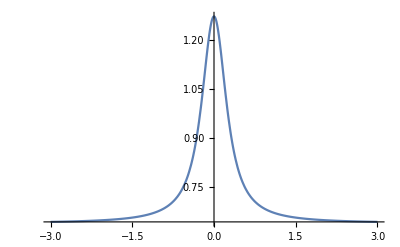

```mathematica
Plot[1/ArcTan[1 + 10 x^2], {x, -3, 3}, PlotRange->Full]
```